```mathematica
ClearAll[r]
```

```mathematica
Ef[r_,M_]=Piecewise[{{0,r.r<1}},-M*r/(r.r)^(3/2)]
Bf[r_,S_]=Piecewise[{{0,r.r<1}},(S-3*S.r/(r.r)*r)/(r.r)^(3/2)]
Bf1[r_,S_]=S/(r.r)^(3/2)
Bf2[r_,S_]=3*S.r/(r.r)*r/(r.r)^(3/2)
```

Piecewise[{{0, r.r<1}, {-(M r)/(r.r)^(3/2), True}}]

Piecewise[{{0, r.r<1}, {(S-(3 r S.r)/(r.r))/(r.r)^(3/2), True}}]

S/(r.r)^(3/2)

(3 r S.r)/(r.r)^(5/2)

```mathematica
StreamPlot3D[Ef[{rx,ry,rz},1],{rx,-2,2},{ry,-2,2},{rz,-2,2},StreamMarkers->"Tube"]
```

-Graphics3D-

```mathematica
StreamPlot3D[Bf[{rx,ry,rz},{0,0,1}],{rx,-2,2},{ry,-2,2},{rz,-2,2},StreamMarkers->"Tube"]
```

-Graphics3D-

## Kraft auf Teilchen in Ebene

```mathematica
$Assumptions = {M>0,ω>0}
ClearAll[x,y,t]
```

{M>0,ω>0}

```mathematica
a[{x_,y_},{vx_,vy_},M_,ω_]=M*(-{x,y}+2/5*ω*{vy,-vx})/(x^2+y^2)^(3/2)
```

{(M (-x+(2 vy ω)/5))/((x^2+y^2)^(3/2)),(M (-y-(2 vx ω)/5))/((x^2+y^2)^(3/2))}

```mathematica
a[{x[t],y[t]},{x'[t],y'[t]},M,ω]//FullSimplify
```

{(M (-x[t]+2/5 ω y'[t]))/((x[t]^2+y[t]^2)^(3/2)),-(M (5 y[t]+2 ω x'[t]))/(5 (x[t]^2+y[t]^2)^(3/2))}

120000

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}

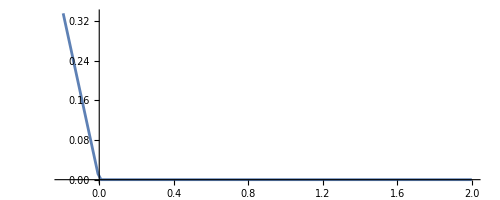

```mathematica
tmax = 120000
sol=NDSolve[{x''[t]==(M (-x[t]+2/5 ω y'[t]))/((x[t]^2+y[t]^2)^(3/2)), y''[t]==-(M (5 y[t]+2 ω x'[t]))/(5 (x[t]^2+y[t]^2)^(3/2)),x'[0]==0,y'[0]==0,x[0]==2,y[0]==0,M==7*10^(-10),ω==1.55*10^(-6)},{x[t],y[t]},{t,0,tmax}][[1]]
ParametricPlot[{x[t],y[t]}/.sol,{t,0,tmax},PlotRange->Full]
```